```mathematica
τ=N [(1+Sqrt[5])/2];
ϕ=N[1+√2];
(* the tangent of the angle of projection *)
θ=Pi/3;
t=Tan[θ];
rot=0;
fib[n_,θ_]:=IntegerPart[Tan[θ]( n+1)]-IntegerPart[Tan[θ](n)];
jump[n_,ρ_,θ_]:=If[fib[n-1,θ]<1,1.,ρ];
```

```mathematica
fib[#,Pi/6]&/@Range[30]
```

{1,0,1,0,1,1,0,1,0,1,0,1,1,0,1,0,1,0,1,1,0,1,0,1,1,0,1,0,1,0}

```mathematica
Clear[h];
h[n_,ρ_,θ_]:=Block[{L=n,tbl,ar},
tbl=Table[{i,i+1}->jump[i,ρ,θ],{i,1,L-1}];
(* periodic boundary conditions *)
(*AppendTo[tbl,{1,L}->ρ];*)
ar=SparseArray[tbl,{L,L}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
n=200;
ρ=0.5;
thetalist=Range[0,Pi/4,.001];
speclist=ParallelMap[Sort[Eigenvalues[#]]&,h[n,ρ,#]&/@thetalist];
```

```mathematica
div=10;
l=Length[speclist];
pts=Table[Point[{i/l,#/div}]&/@speclist[[i]],{i,l}]//Flatten;
```

```mathematica
θm=Max[thetalist];
lines=Table[Line[{{ArcTan[1/q]/θm,-2/div},{ArcTan[1/q]/θm,2/div}}],{q,1,20}];
golden=Line[{{ArcTan[1/GoldenRatio]/θm,-2/div},{ArcTan[1/GoldenRatio]/θm,2/div}}];
```

```mathematica
Graphics[{{PointSize[.001],pts},{Red,lines}}]
```

-Graphics-

```mathematica
ArcTan[1/GoldenRatio]//N
```

0.553574

```mathematica
ArcTan[1]
```

π/4

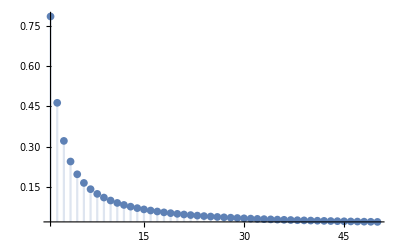

```mathematica
DiscretePlot[ArcTan[1/q],{q,1,50},PlotRange->All]
```

```mathematica
Tan[a+Pi/2]
```

-Cot[a]